```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"];
<<MaTeX`;
MaTeX["x^2"] (*Este bloque echa a andar MaTeX. Para tener tipografia tipo LaTeX*)
```

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
BoltzmannConstant=1.380649*10^-23;(*J/K*)
PlanckConstant = 6.626068*10^-34;(*Js*)
densidad  = 5.317*1/1000*100/1*100/1*100/1;(*Kg*m^-3*)
YoungModule=8.59*10^-5/1*100/1*100/1*100/1;(*N*m^-3*)
ν=1/3;
velocidad=4*10^5*1/100;
altura=200*10^-9;
ancho = 300*10^-9;
largo = 10*10^-6;
rigidez=YoungModule*altura^3/(12*(1-ν^3));
ωRing=(√(rigidez/(densidad*altura)))/ancho^2;
temperatura1 = 1.0;
temperatura2 = 0.8;
```

```mathematica
distribucionBE[frecuencia_,temp_] := 1/(Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)]-1);
distribucionMB[frecuencia_, temp_]:=1/Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)];
```

```mathematica
temperatura=PlanckConstant*velocidad/(BoltzmannConstant*ancho)
```

0.639899

```mathematica
a = 0.01;
aPrime = 0.01;
```

```mathematica
coeficienteB[ω_, k_]:=-(ω+(1-ν)k^2 Cosh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Cos[(√(ω+k^2))/2])*a;
coeficienteBPrima[ω_, k_]:=-(ω+(1-ν)k^2 Sinh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Sin[(√(ω+k^2))/2])*aPrime;
```

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]+
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->20]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= waveNumber^2+offset;
```

```mathematica
amplitudWSim[k_,y_,off_]:=Re[(a*Cosh[√(frecuenciaωSimPositivo[k, off]+k^2)*y]+coeficienteB[frecuenciaωSimPositivo[k, off],k]*Cos[√(frecuenciaωSimPositivo[k, off]-k^2)*y])/√(1/2 (a^2+b^2+b^2 Cos[2 √(k^2+ω)]+(a (8 b Cos[√(k^2+ω)] Sinh[(√(k^2+ω))/2]+a Sinh[√(k^2+ω)]))/(√(k^2+ω)))/.{b->coeficienteB[frecuenciaωSimPositivo[k, off],k], ω->frecuenciaωSimPositivo[k, off]})];
amplitudWAntiSim[k_,y_,off_]:=aPrime*Sinh[√(frecuenciaωAntiSimPositivo[k, off]+k^2)*y]/√(1/2 aPrime^2 (-1+Sinh[√(k^2+ω)]/(√(k^2+ω)))/.{ω->frecuenciaωAntiSimPositivo[k, off]});
```

```mathematica
meanSquaredDisplacement[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]ωRing))*(distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementAnti[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementAntiMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}]
meanSquaredDisplacementAntiBE[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}]
```

```mathematica
meanSquaredDisplacementMB[0.5]
meanSquaredDisplacementMB[0.0]
meanSquaredDisplacementAntiMB[0.5]
meanSquaredDisplacementAntiMB[0.0]
```

3.80159×10^-21

4.31376×10^-21

2.25449×10^-22

0.

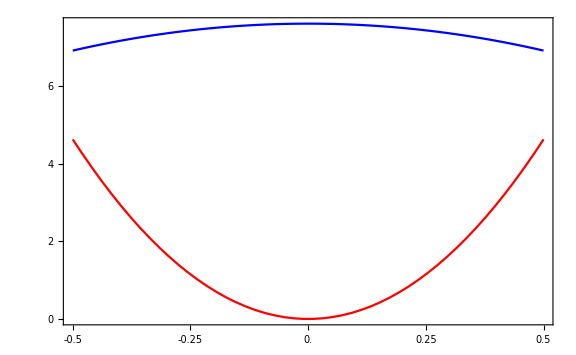

```mathematica
msdSimBE=Plot[{meanSquaredDisplacement[y], meanSquaredDisplacementAntiBE[y]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-16} \\mathrm{m}^{2})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-16,Style[ToString[j], Black]},{j,Range[0,8,2]}], False(* y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["msdBE.pdf",msdSimBE]
```

msdBE.pdf

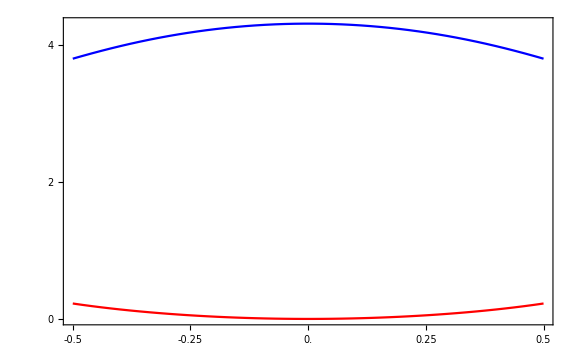

```mathematica
msdSimMB=Plot[{meanSquaredDisplacementMB[y], meanSquaredDisplacementAntiMB[y]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-21} \\mathrm{m}^{2})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-21,Style[ToString[j], Black]},{j,Range[0,5,2]}], False(* y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["msdMB.pdf",msdSimMB]
```

msdMB.pdf

```mathematica
meanSquaredDisplacementMB[0.5]
meanSquaredDisplacementMB[0.0]
```

7.53024×10^-23

7.96392×10^-23

```mathematica
msdSimMB=Plot[meanSquaredDisplacementMB[y],{y, -0.5,0.5},  PlotStyle->Red, ImageSize->Large, GridLines->Automatic,ImagePadding->120,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->{True,True,True,False},FrameStyle->{{Directive[Red, Thick],Directive[Black, Thick]},{Directive[Black, Thick],Directive[Black, Thick]}},
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (10^{-29} \\mathrm{m}^2)", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-29,Style[ToString[j], Red]},{j,Range[2.2,2.40,0.1]}],None(* y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}] (*x axis*),None}
}]
```

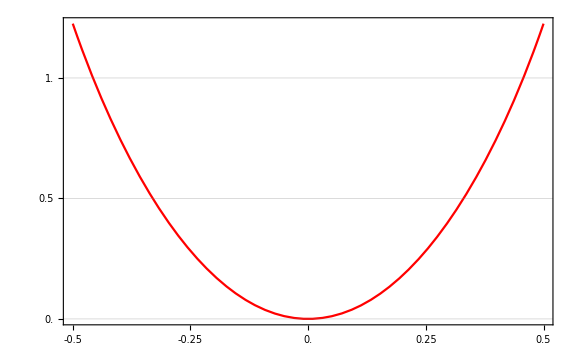

```mathematica
msdAntiSimMB=Plot[meanSquaredDisplacementAntiMB[y],{y, -0.5,0.5},  PlotStyle->Red, ImageSize->Large, GridLines->Automatic,ImagePadding->120,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->{True,True,True,False},FrameStyle->{{Directive[Red, Thick],Directive[Black, Thick]},{Directive[Black, Thick],Directive[Black, Thick]}},
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (10^{-21} \\mathrm{m}^2)", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-21,Style[ToString[j], Red]},{j,Range[0,1,0.5]}],None(* y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}] (*x axis*),None}
}]
```

```mathematica
meanSquaredDisplacementAntiMB[0.5]
```

1.22535×10^-21

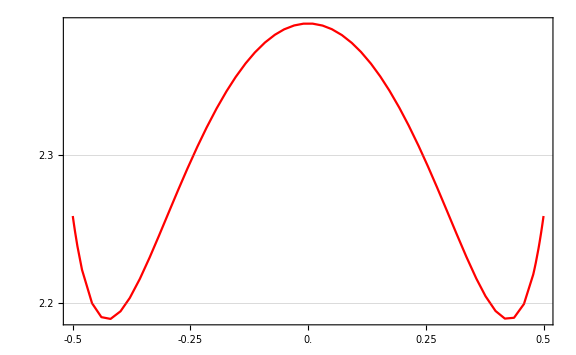
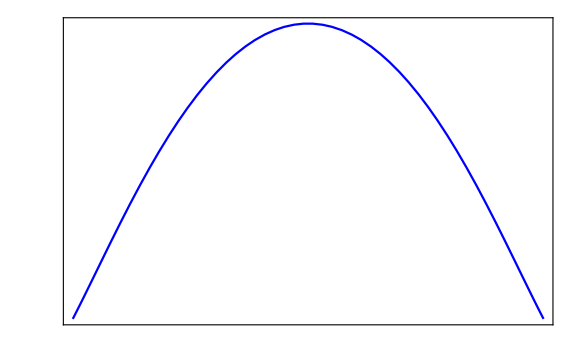

```mathematica
Overlay[{msdSimMB, msdSimBE}]
```

```mathematica
Export["meanQuadraticSymmetric.pdf",%]
```

meanQuadraticSymmetric.pdf

```mathematica
Corriente[y_]:=Sum[(PlanckConstant/(2π)*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}];
CorrienteAnti[y_]:=Sum[(PlanckConstant/(2π)*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2* (distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}];
CorrienteMB[y_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}];
CorrienteAntiMB[y_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2* (distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}]
```

```mathematica
CorrienteMB[0.0]
CorrienteMB[0.5]
CorrienteAntiMB[0.0]
CorrienteAntiMB[0.5]
```

0.000259445

0.000329109

0.

0.000566741

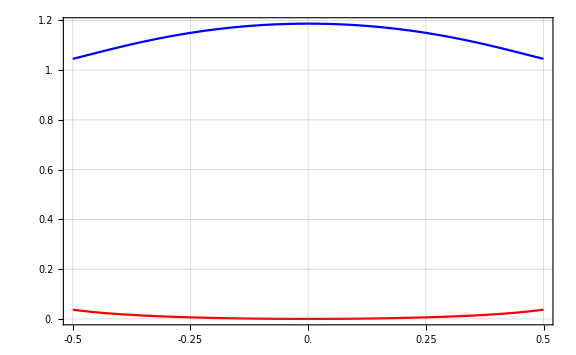

```mathematica
corrientePlotBE=Plot[{Corriente[y], CorrienteAnti[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{J} \\right\\rangle (10^{6} \\mathrm{J}\\mathrm{m}^{-2}\\mathrm{s}^{-1})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^6,Style[ToString[j], Black]},{j,Range[0.0,1.2,0.2]}],False (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["corrienteBE.pdf",corrientePlotBE]
```

corrienteBE.pdf

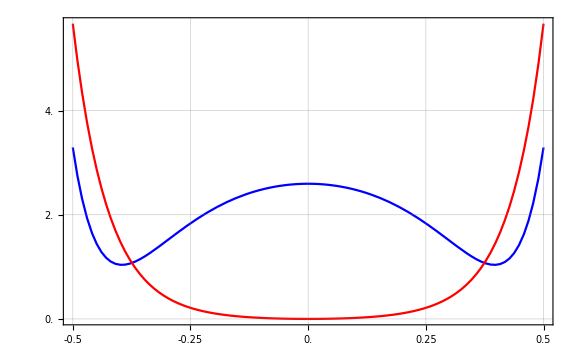

```mathematica
corrientePlotMB=Plot[{CorrienteMB[y], CorrienteAntiMB[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{J} \\right\\rangle (10^{-4} \\mathrm{J}\\mathrm{m}^{-2}\\mathrm{s}^{-1})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-4,Style[ToString[j], Black]},{j,Range[0.0,6,2]}],False (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["corrienteMB.pdf",corrientePlotMB]
```

corrienteMB.pdf

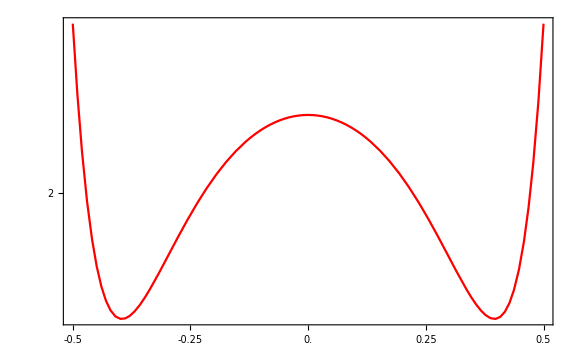

```mathematica
plotCorrienteMB=Plot[CorrienteMB[y],{y,-0.5,0.5},PlotStyle->Red, ImageSize->Large, GridLines->Automatic,ImagePadding->120,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->{True,True,True,False},FrameStyle->{{Directive[Red, Thick],Directive[Black, Thick]},{Directive[Black, Thick],Directive[Black, Thick]}},
FrameLabel->{{MaTeX["\\left\\langle \\hat{J} \\right\\rangle ( 10^{-13}\\mathrm{J}\\mathrm{m}^{-2}\\mathrm{s}^{-1})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-4,Style[ToString[j], Red]},{j,Range[0,6,2]}],None(* y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}] (*x axis*),None}
}]
```

```mathematica
N[2π*30*ancho/largo]
```

5.65487

```mathematica
meanSquareVelocitySimBE[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
```

```mathematica
meanSquareVelocityAntiSimBE[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquareVelocitySimMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
```

```mathematica
meanSquareVelocityAntiSimMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
```

```mathematica
meanSquareVelocitySimBE[0.0]
meanSquareVelocitySimBE[0.5]
meanSquareVelocityAntiSimBE[0.0]
meanSquareVelocityAntiSimBE[0.5]
```

2.81128×10^-6

2.4911×10^-6

0.

1.83731×10^-7

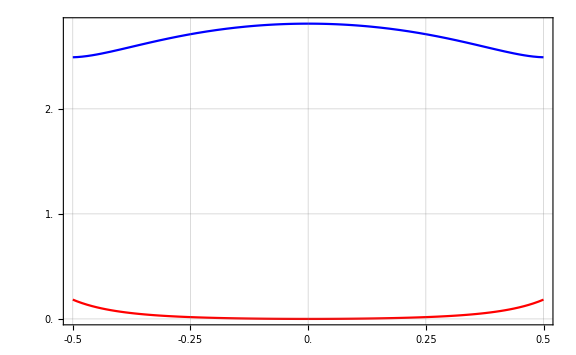

```mathematica
velocityPlotBE=Plot[{meanSquareVelocitySimBE[y], meanSquareVelocityAntiSimBE[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-6} \\mathrm{m}\\mathrm{s}^{-1})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-6,Style[ToString[j], Black]},{j,Range[0.0,3,1]}],False (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["velocidadBE.pdf",velocityPlotBE]
```

velocidadBE.pdf

```mathematica
meanSquareVelocitySimMB[0.0]
meanSquareVelocitySimMB[0.5]
meanSquareVelocityAntiSimMB[0.0]
meanSquareVelocityAntiSimMB[0.5]
```

2.65045×10^-11

2.72036×10^-11

0.

2.33662×10^-11

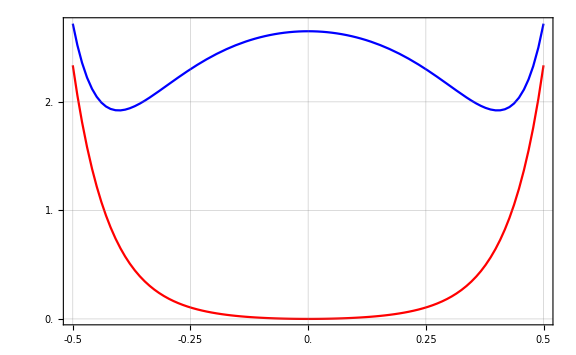

```mathematica
velocityPlotMB=Plot[{meanSquareVelocitySimMB[y], meanSquareVelocityAntiSimMB[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-11} \\mathrm{m}\\mathrm{s}^{-1})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-11,Style[ToString[j], Black]},{j,Range[0.0,3,1]}],False (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

```mathematica
Export["velocityMB.pdf",velocityPlotMB]
```

velocityMB.pdf